# Finite Potential Well

## Even Solutions

```mathematica
m = 0.020;  (*mass of particle*)
U = 3*10^(-65); (*potential energy of surrounding box*)
En = 2*10^(-65); (*energy of particle*)
L = 1; (*length of box*)
h = 6.62607004*10^(-34); (*Planck;s constant*)
hbar = h/(2*Pi);   (* hbar = h/2pi*)

alpha = Sqrt[2*m*(U-En)]/hbar
beta = Sqrt[2*m*En]/hbar

Cl = Cos[beta*L/2]
Xl = Exp[-alpha*L/2]
E0 = (hbar^2)/(2*m)*(Pi/L)^2
ee = En/E0
uu = U/E0
```

5.99727

8.48143

-0.45438

0.049855

2.74405×10^-66

7.2885

10.9327

0.44824

1.49364

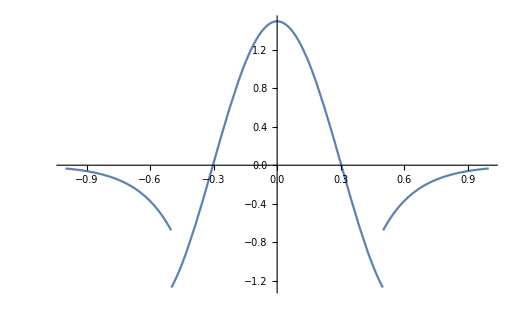

```mathematica
f[x_]:=Piecewise[{{Cl/Xl*Exp[Pi*Sqrt[uu-ee]*x/L],x<-L/2},{Cos[Pi*Sqrt[E]*x/L],(x > -L/2) && (x < L/2)},{Cl/Xl*Exp[Pi*Sqrt[uu-ee]*(-x)/L],x>L/2}}]
inte = NIntegrate[f[x]^2,{x,-∞,∞}]
B = 1/Sqrt[inte]    (*normalisation constant*)
g[x_]:=B*f[x]

Plot[g[x],{x,-L,L}]
```

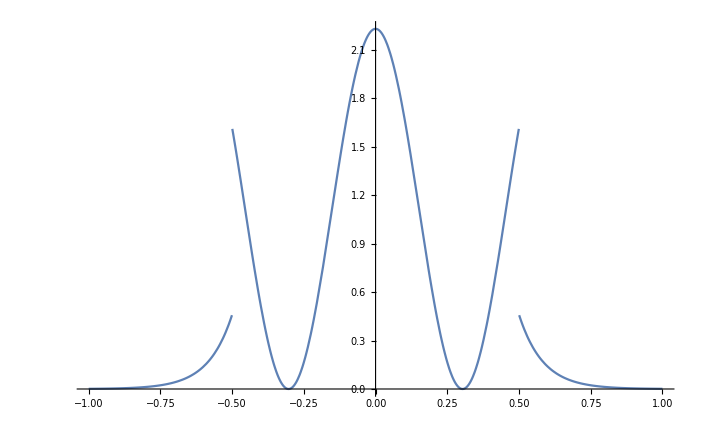

0.923198

```mathematica
Plot[g[x]^2,{x,-L,L}]
a = -L/2;
b = L/2;
NIntegrate[g[x]^2, {x, a, b}]  (*probability of particle staying in box*)
```

## Odd Solutions